# A Mathematica notebook that recreates all figures from the article "Evolutionary adaptation is facilitated by the presence of lethal genotypes" by Viktoryia Blavatska and Bartlomiej Waclaw

### Run this notebook sequentially cell by cell . Running time is less than a minute on Intel Core i7 1.8 GHz and Mathematica version 13.0 The notebook imports data sets generated by C++ programs available from https://github.com/Dioscuri-Centre/quasilethal

```mathematica
SetOptions[{ListPlot,ListLogPlot,ListLinePlot},BaseStyle->26,Frame->True,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}];
```

## Figure 1B

```mathematica
SetDirectory[NotebookDirectory[]];
```

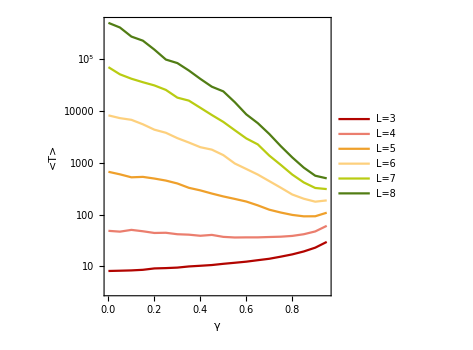

```mathematica
data=(Import["times\\TPosition"<>ToString[#]<>".dat","Table"]) &/@{3,4,5,6,7,8};
ListLogPlot[data,PlotRange->All,FrameLabel->{"γ","<T>"},Joined->True,PlotStyle->ColorData[10,"ColorList"],ImageSize->350,PlotLegends->{"L=3","L=4","L=5","L=6","L=7","L=8"},AspectRatio->1]
```

## Flat landscape (figure not included in the manuscript):

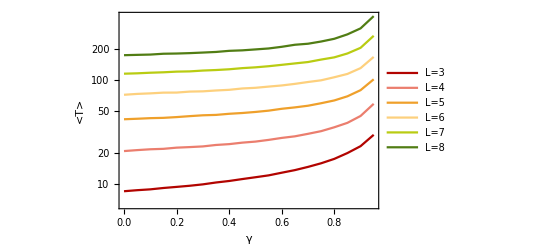

```mathematica
dataflat=(Sort[Import["times_flat\\TflatPosition"<>ToString[#]<>".dat","Table"]]) &/@{3,4,5,6,7,8};
ListLogPlot[dataflat[[All,All,{1,2}]],PlotRange->All,FrameLabel->{"γ","<T>"},Joined->True,PlotStyle->ColorData[10,"ColorList"],ImageSize->400,PlotLegends->{"L=3","L=4","L=5","L=6","L=7","L=8"}]
```

## Figure 1 C

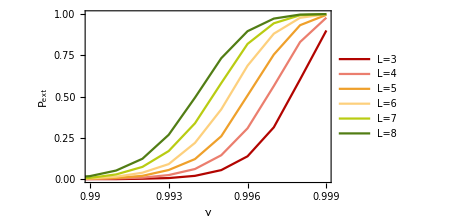

```mathematica
dataPfix=(Sort[Import["ext_probs\\LethalstatisticsPosition"<>ToString[#]<>".dat","Table"]]) &/@{3,4,5,6,7,8};
ListPlot[dataPfix[[All,All,{1,2}]],PlotRange->{{0.99,0.999},All},FrameLabel->{"γ","P_ext"},Joined->True,PlotStyle->ColorData[10,"ColorList"],ImageSize->350,PlotLegends->{"L=3","L=4","L=5","L=6","L=7","L=8","L=9"},FrameTicks->{{Automatic,Automatic},{{0.99,0.993,0.996,0.999},Automatic}}]
```

## Figure 1 D

```mathematica
times={Import["times\\HistogramfirstlethalPosition7mu0.04gama0.00.dat","List"],Import["times\\HistogramfirstlethalPosition7mu0.04gama0.75.dat","List"]};
```

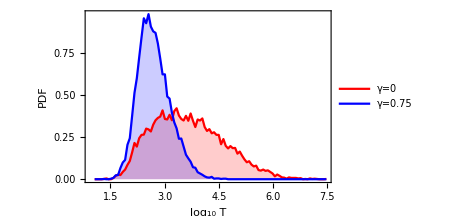

```mathematica
Clear[BinLog]
BinLog[d_]:=Module[{c,min=10,max=3 10^7,dx},dx=(Log[10,max]-Log[10,min])/100.;c=BinCounts[Log[10,d],{Log[10,min],Log[10,max],dx}];MapIndexed[({t, #1/(dx Total[c])}/.t->Log[10,min]+#2[[1]]dx)&,c]]
ListLinePlot[{BinLog[times[[1]]],BinLog[times[[2]]]},PlotRange->All,Filling->Axis,PlotStyle->{Red,Blue},FrameLabel->{"log_10 T","PDF"},ImageSize->350,PlotLegends->{"γ=0","γ=0.75"}]
```

## Figure 2A

### Data generated using the code "directed_evolution_trajectories_both_models.cpp"

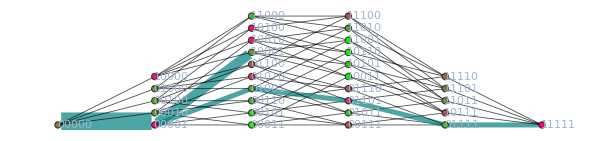

```mathematica
Clear[PlotFL]
PlotFL[fl_,traj_]:=Module[{vert,gr,ypos,vpos,hh,lab,edges,tmp,density,ll=Floor[Log[2,Length[fl]]]},
vert=Table[i,{i,0,2^ll-1}];
gr=AdjacencyGraph[Table[If[HammingDistance[IntegerDigits[vert[[i]],2,ll],IntegerDigits[vert[[j]],2,ll]]==1 ,1,0],{i,Length[vert]},{j,Length[vert]}]];
ypos=Table[0,{i,0,ll}];
vpos=Table[hh=HammingDistance[IntegerDigits[0,2,ll],IntegerDigits[i,2,ll]];ypos[[hh+1]]+=1/4;{2hh,ypos[[hh+1]]},{i,0,2^ll-1}];
lab=Table[IntegerString[vert[[i]],2,ll],{i,Length[vert]}];
edges=EdgeList[gr];


tmp={traj};
density=Table[0,{i,EdgeCount[gr]}];
Module[{x,y,ed=edges},Do[Do[x=tmp[[j,i]]+1;y=tmp[[j,i+1]]+1;Do[If[(ed[[k,1]]==x && ed[[k,2]]==y) || (ed[[k,1]]==y && ed[[k,2]]==x),density[[k]]++;Break[];],{k,EdgeCount[gr]}],{i,Length[tmp[[j]]]-1}],{j,Length[tmp]}]];
density=1.density/Max[density];

Graph[gr,VertexCoordinates->vpos,EdgeStyle->Table[edges[[i]]->If[density[[i]]>0,{Hue[0.5,1,0.5],Thickness[0.03density[[i]]]},{Thickness[0.001],Black}],{i,EdgeCount[gr]}],VertexStyle->Table[i->RGBColor[(fl[[i]]),1-fl[[i]],0.5fl[[i]]],{i,Length[vert]}],VertexLabels->Table[i->Placed["   "<>lab[[i]],Left],{i,Length[vert]}],ImageSize->600]
]
PlotFL[{0.5,0.943512,0.409701,0.0755185,0.333526,0.183589,0.32528,0.655608,0.380707,0.357071,0.772008,0.230591,0.666268,0.740944,0.692913,0.265553,0.860573,0.443792,0.88097,0.0629842,0.896511,0.264696,0.0207809,0.699364,0.276899,0.0333151,0.346812,0.41981,0.730982,0.524687,0.56202,1},{0,1,0,1,17,1,0,1,9,13,15,31}]
```

```mathematica
BarLegend[{RGBColor[#,1-#,0.5#]&,{0,1}},LegendLayout->"Row"]
```

### Load in data for Fig . 2 B - D:

```mathematica
name="model_comparison_L5_K=1000_mu=004_mulet=0_and_19mu.txt";
runs=20;(* runs per FL per model *)

fl=Import["model_comp_on_same_FLs\\FL_"<>name,"Table"];
trajs=Import["model_comp_on_same_FLs\\"<>name,"Table"];
Length[trajs]
Length[fl]

Print["Mean time (non lethal) = ",Mean[trajs[[1;;;;2,4]]]];
Print["Mean time (lethal) = ",Mean[trajs[[2;;;;2,4]]]];

ll=Floor[Log[2,Length[fl[[1]]]]]
```

40000

999

Mean time (non lethal) = 1020.38

Mean time (lethal) = 194.392

5

```mathematica
(* { non-lethal , lethal } *)
times=Transpose[{Mean[#]&/@Partition[trajs[[1;;;;2,4]],runs],Mean[#]&/@Partition[trajs[[2;;;;2,4]],runs]}][[;;-2]];
slowtofast=Ordering[Log[#[[2]]/#[[1]]]&/@times];
Length[slowtofast]
```

999

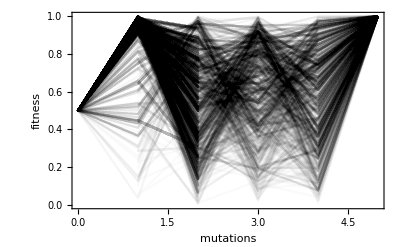

```mathematica
paths1=Table[Table[MapIndexed[{HammingDistance[IntegerDigits[0,2,ll],IntegerDigits[#1,2,ll]],fl[[k,1+#1]]}&,trajs[[2runs (k-1)+2r-1,5;;]]],{r,runs}],{k,slowtofast[[1;;100]]}];
pl1=ListPlot[Flatten[paths1,1],Joined->True,Frame->True,FrameLabel->{"mutations","fitness"},PlotStyle->RGBColor[0,0,0,0.02]]
```

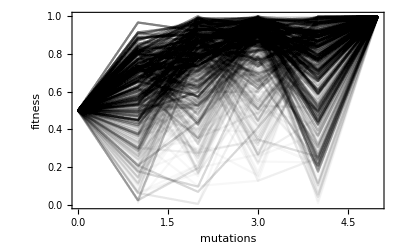

```mathematica
paths2=Table[Table[MapIndexed[{HammingDistance[IntegerDigits[0,2,ll],IntegerDigits[#1,2,ll]],fl[[k,1+#1]]}&,trajs[[2runs (k-1)+2r-1,5;;]]],{r,runs}],{k,slowtofast[[-100;;-1]]}];
pl2=ListPlot[Flatten[paths2,1],Joined->True,Frame->True,FrameLabel->{"mutations","fitness"},PlotStyle->RGBColor[0,0,0,0.03]]
```

## Figure 2 B

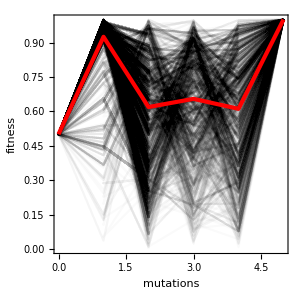

```mathematica
Show[pl1,ListPlot[{#[[1,1]],Mean[#[[All,2]]]}&/@Gather[Flatten[paths1,2],(#1[[1]]==#2[[1]])&],PlotStyle->{Red,AbsoluteThickness[3]},Joined->True,Frame->True,FrameLabel->{"mutations","average fitness"}],AspectRatio->1,ImageSize->300]
```

## Figure 2 C

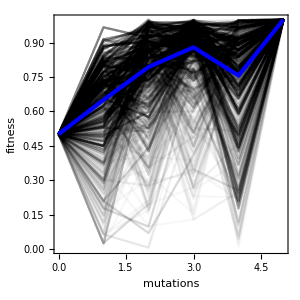

```mathematica
Show[pl2,ListPlot[{#[[1,1]],Mean[#[[All,2]]]}&/@Gather[Flatten[paths2,2],(#1[[1]]==#2[[1]])&],PlotStyle->{Blue,AbsoluteThickness[3]},Joined->True,Frame->True,FrameLabel->{"mutations","average fitness"}],AspectRatio->1,ImageSize->300]
```

```mathematica
paths3=Table[Table[MapIndexed[{HammingDistance[IntegerDigits[0,2,ll],IntegerDigits[#1,2,ll]],fl[[k,1+#1]]}&,trajs[[2runs (k-1)+2r,5;;]]],{r,runs}],{k,slowtofast[[1;;100]]}];
```

```mathematica
paths4=Table[Table[MapIndexed[{HammingDistance[IntegerDigits[0,2,ll],IntegerDigits[#1,2,ll]],fl[[k,1+#1]]}&,trajs[[2runs (k-1)+2r,5;;]]],{r,runs}],{k,slowtofast[[-100;;-1]]}];
```

## Figure 2 D

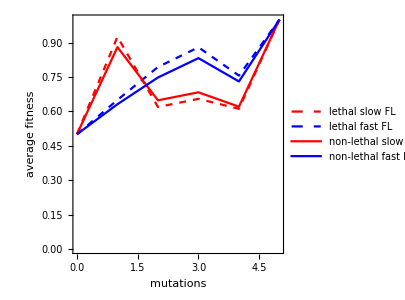

```mathematica
ListPlot[{{#[[1,1]],Mean[#[[All,2]]]}&/@Gather[Flatten[paths1,2],(#1[[1]]==#2[[1]])&],{#[[1,1]],Mean[#[[All,2]]]}&/@Gather[Flatten[paths2,2],(#1[[1]]==#2[[1]])&],{#[[1,1]],Mean[#[[All,2]]]}&/@Gather[Flatten[paths3,2],(#1[[1]]==#2[[1]])&],{#[[1,1]],Mean[#[[All,2]]]}&/@Gather[Flatten[paths4,2],(#1[[1]]==#2[[1]])&]},PlotStyle->{{Dashed,Red},{Dashed,Blue},Red,Blue,},Joined->True,Frame->True,FrameLabel->{"mutations","average fitness"},PlotLegends->{"lethal slow FL","lethal fast FL","non-lethal slow FL","non-lethal fast FL"},AspectRatio->1,ImageSize->300]
```

## Figure 3B

```mathematica
tts3=Select[Import["1d_model\\Tversion3.dat","Table"],(Length[#]>0&)]
tts4=Select[Import["1d_model\\Tversion4.dat","Table"],(Length[#]>0&)]
```

{{0.,653.612},{0.05,617.243},{0.1,593.245},{0.15,563.418},{0.2,532.959},{0.25,506.316},{0.3,468.904},{0.35,430.316},{0.4,400.629},{0.45,367.567},{0.5,332.691},{0.55,298.446},{0.6,265.005},{0.65,237.345},{0.7,207.291},{0.75,176.871},{0.8,151.33},{0.85,120.914},{0.9,90.7951},{0.95,72.8493}}

{{0.,74949.7},{0.05,67708.4},{0.1,60022.},{0.15,53100.},{0.2,48390.8},{0.25,42539.3},{0.3,35373.1},{0.35,31977.9},{0.4,26939.8},{0.45,21284.6},{0.5,17495.8},{0.55,14494.4},{0.6,12154.1},{0.65,8361.27},{0.7,6694.01},{0.75,4707.63},{0.8,2965.67},{0.85,1712.9},{0.9,706.732},{0.95,276.353}}

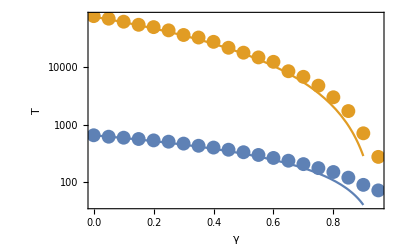

```mathematica
Clear[δ,kk]
Show[ListLogPlot[{tts3,tts4},PlotStyle->AbsolutePointSize[10]],LogPlot[{4δ/(kk μ^2 (1-δ))  (2δ(1-γ-μ)/((1-δ)μ))^(l-2)/.{l->3,δ->0.7,μ->0.04,kk->1000},4δ/(kk μ^2 (1-δ))  (2δ(1-γ-μ)/((1-δ)μ))^(l-2)/.{l->4,δ->0.7,μ->0.04,kk->1000}},{γ,0,0.9},PlotRange->All],PlotRange->All,Axes->False,FrameLabel->{"γ","T"},ImageSize->{Automatic,300}]
```

## Figure 4 A

{{{0,0.2946},{1,0.6892},{2,0.0162}},{{0,0.1004},{1,0.4959},{2,0.4033},{3,0.0004}},{{0,0.0332},{1,0.5343},{2,0.1663},{3,0.2662}},{{0,0.0101},{1,0.3918},{2,0.377},{3,0.0549},{4,0.1662}},{{0,0.0026},{1,0.3955},{2,0.3785},{3,0.1035},{4,0.0186},{5,0.1013}},{{0,0.0013},{1,0.3036},{2,0.3806},{3,0.2144},{4,0.0314},{5,0.0069},{6,0.0618}}}

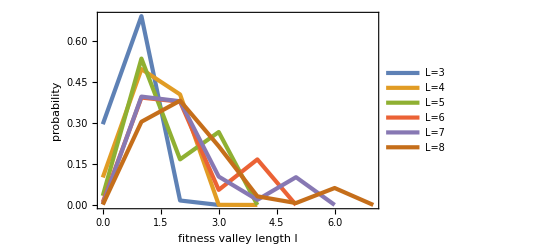

```mathematica
(* histograms of min length of fitness valley *)
pps=Table[Import["path_stats\\Problminposition"<>ToString[ll]<>".dat"],{ll,3,8}]
ListPlot[Append[#,{#[[-1,1]]+1,0}]&/@pps,Joined->True,FrameLabel->{"fitness valley length l","probability"},PlotLegends->{"L=3","L=4","L=5","L=6","L=7","L=8","L=9"},ImageSize->{Automatic,300},PlotStyle->AbsoluteThickness[3]]
```

## Figure 4 B

{{3,3.64896},{4,1.1936},{5,0.2619},{6,0.0567388},{7,0.0118125},{8,0.00251395}}

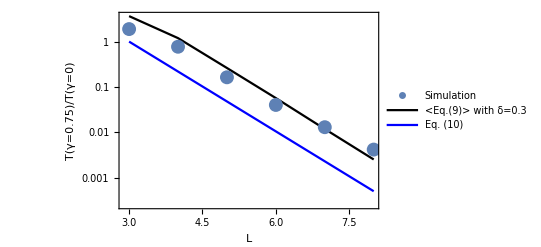

```mathematica
δ=0.3;kk=1000;
Clear[Tadapt,k] 
Tadapt[k_,γ_,δ_,μ_,l_]:=(4δ/(k(1-δ)μ^2))(2δ(1-γ-μ)/(μ(1-δ)))^(l-2)
Table[{ll,pp=pps[[ll-2]];t1=Total[#[[2]]Tadapt[kk,0.75,δ,0.04,0+#[[1]]]&/@pp]/Total[pp[[All,2]]];
t2=Total[#[[2]]Tadapt[kk,0,δ,0.04,0+#[[1]]]&/@pp]/Total[pp[[All,2]]];(*Print["L=",ll," t1=",t1," t2=",t2];*)
t1/t2},{ll,3,8}]
ListLogPlot[{MapIndexed[{#2[[1]]+2,#[[2,2]]/#[[1,2]]}&,data[[All,{1,16}]]],%,Table[{ll,((1-γ-μ)/(1-μ))^(l-2)}/.{l->ll-1,γ->0.75,μ->0.04},{ll,3,8}]},Joined->{False,True,True},PlotStyle->{AbsolutePointSize[10],Black,Blue},Frame->True,FrameLabel->{"L","T(γ=0.75)/T(γ=0)"},PlotLegends->{"Simulation","<Eq.(9)> with δ="<>ToString[δ],"Eq. (10)"},ImageSize->{Automatic,300}]
```